## Simple Task 11 Valerie Richmond CPS371 8am

### i.

```mathematica
lifeExp=CountryData["Countries", "LifeExpectancy"];
povFrac=CountryData["Countries", "PovertyFraction"];
```

```mathematica
pointList={};
For[i=1, i<Length[lifeExp], i++, AppendTo[pointList, {lifeExp[[i]], povFrac[[i]]}]];
```

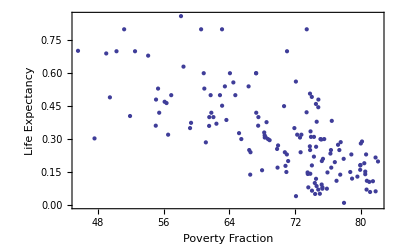

```mathematica
ListPlot[pointList, Frame-> True,FrameLabel->{{"Life Expectancy"," "},{"Poverty Fraction"," "}} ]
```

### ii.

The life expectancy is higher for countries with a lower poverty fraction. This can be explained by the fact that living in poverty often means that one can’t afford health care or good nutritious meals, both of which would contribute to longevity. Also, a country with a high poverty fraction is most likely poor and so could not provide health care to its people.

### iii.

```mathematica
pointList=Select[pointList, NumberQ[#[[1]]]&& NumberQ[#[[2]]] &];
```

```mathematica
Clear[x];
fxn=Fit[pointList, {1,x}, x]
```

1.37822-0.0151402 x

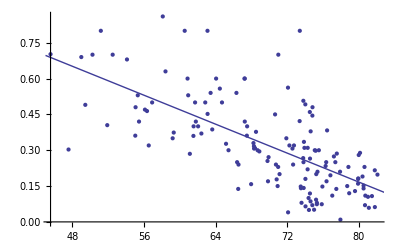

```mathematica
Show[ListPlot[pointList], Plot[fxn, {x,45,85}]]
```

The relationship between the poverty fraction and life expectancy is linear because the more people living in poverty a country has, the more pull down on the life expectancy that country has, and that relationship is a simple proportion.

```mathematica
Clear[a,x,b];
model=a*x+b;
statInfo=NonlinearModelFit[pointList,model,{a,b},x];
statInfo[{"RSquared"}]
```

{0.859677}

The R squared value is relatively close to 1, indicating that the model is a good fit. The data is pretty spaced out and so every model would have R squared values at least a little below 1.